```mathematica
(*Import all patient data*)
ro=ResourceObject["Patient Medical Data for Novel Coronavirus COVID-19"];
rd=ResourceData["Patient Medical Data for Novel Coronavirus COVID-19"];
(*This next export import step can be skipped but I found the data in this form slightly easier to deal with. Note that imp becomes a table of strings only*)
Export["data.csv",rd];
imp=Import["data.csv"];
(*Turn it into an expression and simplify some of the datatypes*)
data1=ToExpression[imp]/.{Entity["AdministrativeDivision",{m_,n_}]->{m,n},Entity["Country",m_]->m,TemporalData[TimeSeries,{{m_},n_,1,{"Continuous",1},{"Discrete",1},1,{ValueDimensions->1,DateFunction->Automatic,ResamplingMethod->{"Interpolation",InterpolationOrder->1}}},True,12.]->m,Entity["Gender",m_]->m,Entity["City",{m_,n_,o_}]->{m,n,o},DateObject[m_,"Day","Gregorian",-6.]->m,Missing["NotAvailable"]->"NA"};
(*This takes one of the examples and lists all of the patient data and adds to it the mean temperature in that person's location between Feb and March 2019. Including a lot of them will take a long time.*)
(*upto gives the first 'upto' patients*)
upto=10
exampledata=data1[[2;;upto]];
withtemp=Join[{Join[data1[[1]],{"average temperature from Feb to March 2019"}]},Table[Join[exampledata[[n]],{Mean[Normal[WeatherData[exampledata[[n,6]],"MeanTemperature", {{2019, 2, 1}, {2019,3,1}, "Day"}][[2,1,1]]][[;;,1]]]}],{n,Length[exampledata]}]];
TableForm[%]
Export["withtemp.csv",withtemp]
```

```mathematica
(*This takes one of the examples and lists all of the patient data and adds to it the mean temperature in that person's location between Feb and March 2019.*)
(*upto gives the first 'upto' patients*)
upto=10
exampledata=data1[[2;;upto]];
withtemp=Join[{Join[data1[[1]],{"average temperature from Feb to March 2019"}]},Table[Join[exampledata[[n]],{Mean[Normal[WeatherData[exampledata[[n,6]],"MeanTemperature", {{2019, 2, 1}, {2019,3,1}, "Day"}][[2,1,1]]][[;;,1]]]}],{n,Length[exampledata]}]];
TableForm[%]
Export["withtemp.csv",withtemp]
```

10

Age | Sex | City | AdministrativeDivision | Country | GeoPosition | DateOfOnsetSymptoms | DateOfAdmissionHospital | DateOfConfirmation | Symptoms | LivesInWuhan | LivesInWuhanComment | TravelHistoryDates | TravelHistoryLocation | ReportedMarketExposure | ReportedMarketExposureComment | ChronicDiseaseQ | ChronicDiseases | SequenceAvailable | DischargedQ | DeathQ | DateOfDeath | DateOfDischarge | average temperature from Feb to March 2019
30 | Male | Hefei
Anhui
China | Anhui
China | China | GeoPosition[{31.6539,117.829}] | 2020
1
18 | 2020
1
20 | 2020
1
22 | NA | True | NA | 2020 | 1 | 17 | Wuhan | Hubei | China | NA | NA | NA | NA | NA | NA | NA | NA | NA | 4.81655
47 | Male | Hefei
Anhui
China | Anhui
China | China | GeoPosition[{31.8283,117.225}] | 2020
1
10 | 2020
1
21 | 2020
1
23 | NA | False | NA | 2020 | 1 | 10 | Wuhan | Hubei | China | NA | NA | NA | NA | NA | NA | NA | NA | NA | 3.96034
49 | Male | Hefei
Anhui
China | Anhui
China | China | GeoPosition[{31.8283,117.225}] | 2020
1
15 | 2020
1
20 | 2020
1
23 | NA | False | NA | 2020 | 1 | 10 | Wuhan | Hubei | China | NA | NA | NA | NA | NA | NA | NA | NA | NA | 3.96034
47 | Female | Hefei
Anhui
China | Anhui
China | China | GeoPosition[{31.8283,117.225}] | 2020
1
17 | 2020
1
20 | 2020
1
23 | NA | False | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | 3.96034
50 | Female | Hefei
Anhui
China | Anhui
China | China | GeoPosition[{31.8283,117.225}] | 2020
1
10 | 2020
1
21 | 2020
1
23 | NA | False | NA | 2020 | 1 | 7 | Wuhan | Hubei | China | NA | NA | NA | NA | NA | NA | NA | NA | NA | 3.96034
NA | NA | Luan
Anhui
China | Anhui
China | China | GeoPosition[{31.7345,116.521}] | NA | NA | 2020
1
24 | pneumonia | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | NA | 3.3731
42 | Female | Fuyang
Anhui
China | Anhui
China | China | GeoPosition[{32.8905,115.815}] | 2020
1
21 | 2020
1
21 | 2020
1
22 | fever | False | NA | 2020 | 1 | 19 | Wuhan | Hubei | China | NA | NA | NA | NA | NA | NA | NA | NA | NA | 3.50379
NA | Female | Huaibei
Anhui
China | Anhui
China | China | GeoPosition[{33.9441,116.791}] | NA | NA | 2020
1
25 | NA | False | NA | 2020 | 1 | 13 | Wuhan | Hubei | China | NA | NA | NA | NA | NA | NA | NA | NA | NA | 3.41862
59 | Female | Huainan
Anhui
China | Anhui
China | China | GeoPosition[{32.623,117.012}] | 2020
1
19 | 2020
1
24 | 2020
1
26 | fever | True | NA | 2020 | 1 | 22 | Wuhan | Hubei | China | NA | NA | NA | NA | NA | NA | NA | NA | NA | 3.96034

withtemp.csv

```mathematica
Export["patientdata.csv",%]
```

```mathematica
(*This is epidemiological data, not individual patient data.*)
```

```mathematica
ro1=ResourceObject["Epidemic Data for Novel Coronavirus COVID-19"];
rd1=ResourceData["Epidemic Data for Novel Coronavirus COVID-19"];
Export["dataepidemic.csv",rd1];
imp1=Import["dataepidemic.csv"];
data2=ToExpression[imp1]/.{Entity["AdministrativeDivision",{m_,n_}]->{m,n},Entity["Country",m_]->m,TemporalData[TimeSeries,{{m_},n_,1,{"Continuous",1},{"Discrete",1},1,{ValueDimensions->1,DateFunction->Automatic,ResamplingMethod->{"Interpolation",InterpolationOrder->1}}},True,12.]->m,ConfirmedCases->"Confirmed Cases starting from 22nd of Jan 2020",RecoveredCases->"Recovered Cases starting from 22nd of Jan 2020",Missing["NotAvailable"]->"NA"};
Export["epidemicdata.csv",%]
```

epidemicdata.csv

```mathematica
(*These are all the symptoms of all patients taken together.*)
data1[[2;;]][[;;,10]];
allsymptoms=Flatten[%]//Union
```

{acute coronary syndrome,acute left heart failure,acute respiratory viral infection,anhelation,asymptomatic,body soreness,chest discomfort,chest distress,chest pain,chest tightness,chills,cold symptoms,cough,diarrhea,discomfort,dizziness,dry cough,dyspnea,emesis,expectoration,fatigue,fever,flu-like symptoms,gasp,grasp,headache,high fever,joint pain,lack of energy,lesions on chest radiographs,little sputum,low fever,mild cough,mild symptoms,mild symptoms of pneumonia,muscular soreness,muscular stiffness,myalgias,NA,nasal congestion,nausea,no fever,obnubilation,other symptoms,pharyngalgia,pharyngeal discomfort,pharynx,physical discomfort,pleural effusion,pleuritic chest pain,pneumonia,pneumonitis,primary myelofibrosis,respiratory distress,respiratory problems,respiratory stress,respiratory symptoms,rhinorrhoea,rigor,runny nose,severe cough,shortness of breath,sneezing,somnolence,sore limbs,sore muscle,sore throat,sputum,unwell,weakness,wheezing}

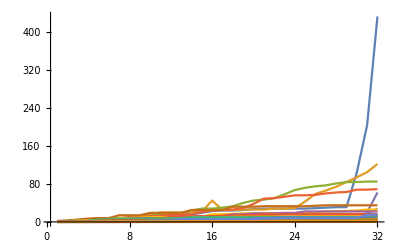

```mathematica
(*The timeseries for each country/region*)
timeseries={#[[2]],ToExpression[#[[4]]][[2,1,1]]}&/@imp1[[2;;]];
ListLinePlot[DeleteCases[%,{"Entity[\"Country\", \"China\"]",__}|{"Missing[\"NotACountryDiamondPrincessCruiseShip\"]",__}][[;;,2]],PlotRange->All]
```

```mathematica
(*Go through the timeseries data, not including China*)DeleteCases[timeseries,{"Entity[\"Country\", \"China\"]",__}|{"Missing[\"NotACountryDiamondPrincessCruiseShip\"]",__}];
Manipulate[ListLinePlot[%[[n,2]],PlotRange->All,PlotLabel->%[[n,1]]],{n,1,Length[%],1}]
```

```mathematica
(*See the number of patients in a given country after first case was reported for any given day.*)
uptoday[n_]:=DeleteCases[{#[[1]],With[{x=DeleteCases[#[[2]],0]},If[Length[x]>n,x[[n]],0]]}&/@DeleteCases[timeseries,{"Entity[\"Country\", \"China\"]",__}|{"Missing[\"NotACountryDiamondPrincessCruiseShip\"]",__}],{_,0}]
```

```mathematica
Manipulate[Histogram[uptoday[n][[;;,2]],{5},PlotRange->{{0,100},{0,30}}],{n,1,30,1}]
```